```mathematica
(*Initialisation - Run first*)
SetEnvironment["OMP_NUM_THREADS"->"8"]
(*Replace the following with the appropriate pathways for your device*)
(*Import["/Users/questuser/Documents/QuESTlink/Link/QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["/Users/questuser/Documents/Kathryn/quest_link"]; (*Creating QuEST environment*)
Import["/Users/questuser/Documents/Kathryn/RydbergInstaSWAPGerardCZ.wl"]; (*Configuration File*)
data=Import["/Users/questuser/Documents/Kathryn/SU4Gates9Qubits.csv"]; (*Imported gates from Qiskit*)*)
Import["C:\\Users\\KitKa\\QuESTlink\\Link\\QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["C:\\Users\\KitKa\\QuESTlink\\quest_link.exe"];(*Creating QuEST environment*)Import["C:\\Users\\KitKa\\QuESTlink\\Rydberg Custom Gates Custom SWAP Windows Vers.wl"];(*Configuration File*)data=Import["C:\\Users\\KitKa\\OneDrive\\Documents\\Wolfram Mathematica\\SU4Gates9Qubits.csv"];
userconfig=<|
NQubits-> 9,
QubitLocations->Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{0,2,0},{1,2,0},{2,0,0},{2,1,0},{2,2,0}}}],
(* blockade radius in μm*)
BlockadeRadius->10,
(* inter-atomic separation in μm. This will be the unit of the lattice given in qubitLocations *)
UnitLattice->1,
(* T1=τvac/nqubits in μs *)
VacuumLifeTime->4*10^6,
(* the γ noise on theq initialization *)
LeakProbInit->0.007,
(* duration on the initialization *)
DurInit->300,
(* measurement induces atom loss afterward *)
FidMeas-> 100,
DurMeas-> 2*10^4,
(* the increasing chance of atom loss due to measurement, in percent *)
AtomLossMeas-> 0,
(* mostly used in the single qubit noise, unit μs. It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.49*10^6,
(* leak probability of implementing multi-qubit gates *)
LeakProbCZ-> <|01-> 0.001,11->0.001 |>,
(* Rabi frequency, MHz *)
Ω->1,
(* fidelity of swap operation *)
FidSWAP->99.7
|>;
RydDev=CreateRydbergDevice[userconfig];
RydDev[InitLocations]
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations];
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
```

-Graphics3D-

```mathematica
Fraction[a_,b_]:=a/b
KetList[NQ_]:=Table[ToExpression@StringSplit[IntegerString[i,2,NQ],""],{i,0,2^NQ-1,1}]
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure*)

MeasErrors[QubitList_]:=Table[Subscript[U,QubitList[[i]]][{{0.9997,0},{0,1.0003}}],{i,1,Length[QubitList]}]
```

```mathematica
KetList[3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}]

-Graphics-

U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]

{X_0,X_1,X_2,H_0,X_0,U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}],X_0,H_0,X_0,X_1,X_2}

{X_0,X_1,X_2,H_0,X_0,U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}],X_0,H_0,X_0,X_1,X_2}

{H_0,U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}],H_0}

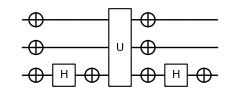

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)

-Graphics-

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
Toff=Subscript[U, 0,1,2][{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}]
DrawCircuit[{Toff}]
CCZ=Subscript[U, 0,1,2][{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]
CCZCirc={Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[H, 0],Subscript[X, 0],Toff,Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2]}
ToffCirc={Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[H, 0],Subscript[X, 0],CCZ,Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2]}
CCZClifCirc={Subscript[H, 0],Toff,Subscript[H, 0]}(*{Subscript[X,1],Subscript[X,2],Subscript[X, 0],CCZ,Subscript[X, 0],Subscript[X,1],Subscript[X,2]}*)
DrawCircuit[ToffCirc]
CalcCircuitMatrix[{Toff}]//MatrixForm
CalcCircuitMatrix[ToffCirc]//MatrixForm
DrawCircuit[CCZCirc]
CalcCircuitMatrix[{CCZ}] //MatrixForm
CalcCircuitMatrix[CCZCirc] // MatrixForm
CalcCircuitMatrix[CCZClifCirc]//MatrixForm
```

```mathematica
{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
InitCirc[NQ_]:=Table[Subscript[Init, b],{b,0,NQ-1,1}]
GroverIteration3Q[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed],1]},
Xs=Table[XTrans[XIndices[[j,1]]-1],{j,1,Length[XIndices]}];
Flatten[{Xs,Subscript[CCZ, 0,1,2],Xs,HTrans[0],HTrans[1],HTrans[2],Subscript[CCZ, 0,1,2],HTrans[0],HTrans[1],HTrans[2]}]]
Table[DrawCircuit[GroverIteration3Q[KetList[3][[i]]]],{i,1,8}]
KetList[3]
GroversAlg3Q=Table[SearchSeeds=KetList[3];
ρ=CreateDensityQureg[3];
(*InitZeroState[ρ];*)
InitialisationCirc=ExtractCircuit[GetCircuitSchedule[Join[InitCirc[3],HTrans[0],HTrans[1],HTrans[2]],RydDev,ReplaceAliases->True]];
ApplyCircuit[ρ,InitialisationCirc];
Gr=ExtractCircuit[GetCircuitSchedule[GroverIteration3Q[SearchSeeds[[i]]],RydDev,ReplaceAliases->True]];
ApplyCircuit[ρ,Join[Gr,Gr]];CalcProbOfAllOutcomes[ρ,{0,1,2}],{i,1,8}]

DestroyAllQuregs[];
```

```mathematica
XTrans[i_]:={Subscript[Rx, i][Pi]};
HTrans[i_]:={Subscript[Ry, i][Pi/2],Subscript[Rx, i][Pi]};
ToffSandBread[t_,c1_,c2_]:={Subscript[Ry, t][-Pi/2],Subscript[Rx, t][-Pi],Subscript[Rx, c1][Pi],Subscript[Rx, c2][Pi]}
```

```mathematica
Toff[t_,c1_,c2_]:=Subscript[U, t,c1,c2][{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}]
CCZGate[t_,c1_,c2_]:=Subscript[U, t,c1,c2][{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]
```

```mathematica
ToffRyd[t_,c1_,c2_]:={{Subscript[X, t],Subscript[X, c1],Subscript[X, c2],Subscript[H, t],Subscript[X, t],CCZGate[t,c1,c2],Subscript[X, t],Subscript[H, t],Subscript[X, t],Subscript[X, c1],Subscript[X, c2]}}
```

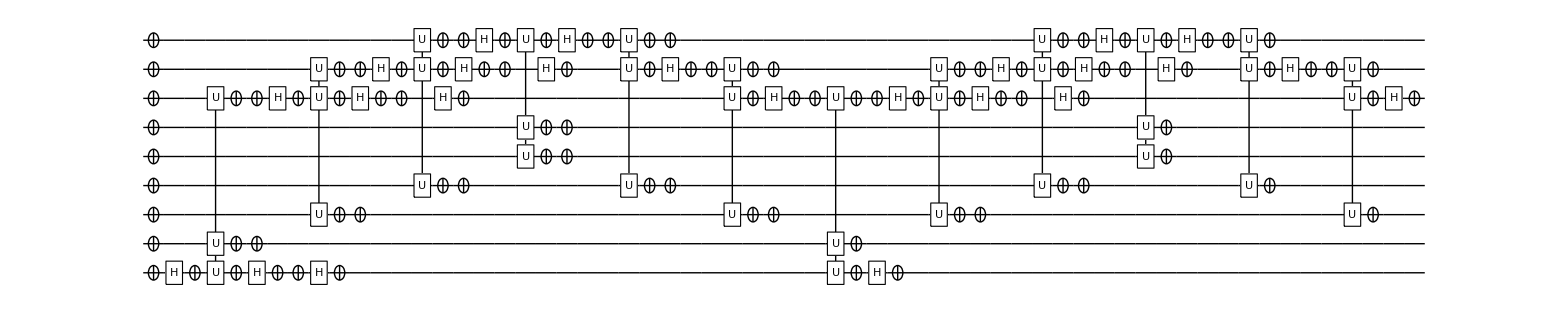

0

```mathematica
(*C4ZMat=DiagonalMatrix[Join[{1},Table[-1,{i,1,2^5-1}]]];
C4XMat=CalcCircuitMatrix[{Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[U, 0,1,2,3,4][C4ZMat],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4]}];
C4XCirc={Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[U, 0,1,2,3,4][C4ZMat],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4]};
C4ZCirc={Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[U, 0,1,2,3,4][C4XMat],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4]};
C4XCircToff={Toff[0,6,1],Toff[6,7,2],Toff[7,8,3],Toff[8,4,5],Toff[7,8,3],Toff[6,7,2],Toff[0,6,1],Toff[6,7,2],Toff[7,8,3],Toff[8,4,5],Toff[7,8,3],Toff[6,7,2]};*)
C4XCircCCZ=Flatten[{ToffRyd[0,6,1],ToffRyd[6,7,2],ToffRyd[7,8,3],ToffRyd[8,4,5],ToffRyd[7,8,3],ToffRyd[6,7,2],ToffRyd[0,6,1],ToffRyd[6,7,2],ToffRyd[7,8,3],ToffRyd[8,4,5],ToffRyd[7,8,3],ToffRyd[6,7,2]}];
DrawCircuit[C4XCircCCZ]
Length[C5ZMat]
```

```mathematica
?Delete
```

```mathematica
XTrans[i_]:={Subscript[Rx, i][Pi]};
HTrans[i_]:={Subscript[Ry, i][Pi/2],Subscript[Rx, i][Pi]};
HXTrans[q_]:=Subscript[Ry, q][Pi/2]
XHTrans[q_]:=Subscript[Ry, q][-Pi/2]
XHXTrans[q_]:={Subscript[Ry, q][-Pi/2],Subscript[Rx, q][-Pi]}
HXHTrans[q_]:={Subscript[Ry, q][-Pi],Subscript[Rx, q][-Pi]}
Subscript[CCZDecomp,t_,c1_,c2_]:=
```

```mathematica
KetList[5][[1]][[2;;]]
```

{0,0,0,0}

```mathematica
CliffCCZRyd={HXTrans[0],HXTrans[0],Table[XTrans[i],{i,1,8}],Subscript[CCZ, 0,6,1],HXTrans[6],Subscript[CCZ, 7,6,2],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,5,4] XHTrans[8],Subscript[CCZ, 8,7,3]}
GroverIteration3Q[SearchSeed_]:=Module[{XIndices=Join[Position[Reverse[SearchSeed][[1]],1],Position[Reverse[SearchSeed][[2;;]],0]]},
Xs=Table[XTrans[XIndices[[j,1]]-1],{j,1,Length[XIndices]}];
Flatten[{Xs,Subscript[CCZ, 0,1,2],Xs,HTrans[0],HTrans[1],HTrans[2],Subscript[CCZ, 0,1,2],HTrans[0],HTrans[1],HTrans[2]}]]
```

```mathematica
?Replace
```

```mathematica
Print[KetList[6][[1]]]
C5XTranspiled=Flatten[{Table[XTrans[i],{i,1,8}],XTrans[0],HXTrans[0],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],,XHTrans[0],XTrans[0],Table[XTrans[i],{i,1,8}]}];
C5ZCliffTrans=Join[HTrans[0],C5XTranspiled,HTrans[0]];
GroverOracle6D3A[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed][[2;;]],1]},
If[Reverse[SearchSeed][[1]]==0,XStart={XTrans[0],HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0],XTrans[0]},
XStart={HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0]}];
Xs=Flatten[Table[XTrans[XIndices[[j,1]]],{j,1,Length[XIndices]}]];
(*Print[Xs];*)
Flatten[{XStart,Xs,Table[XTrans[i],{i,6,8}],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Xs,XEnd}]]
GroverDiffusion6D3A=Flatten[{Table[HTrans[i],{i,0,5}],Table[XTrans[i],{i,6,8}],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Table[HTrans[i],{i,0,5}]}];





GroversAlg6D3A[SearchSeed_]:=Flatten[Join[Table[HTrans[i],{i,0,5}],Table[{GroverOracle6D3A[SearchSeed],GroverDiffusion6D3A},{j,1,8}]]]
Table[(*Print[i];*)SearchSeed=KetList[6][[i]];
ρ=CreateDensityQureg[9];
InitZeroState[ρ];
ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[GroversAlg6D3A[SearchSeed],RydDev,ReplaceAliases->True]]];
CalcProbOfAllOutcomes[ρ,{0,1,2,3,4,5}][[i]],{i,1,64}]


(*DrawCircuit[GroverOracle6D3A[KetList[6][[1]]]]
DrawCircuit[ExtractCircuit[GetCircuitSchedule[C5XTranspiled,RydDev,ReplaceAliases->True]]]*)
(*ExtractCircuit[GetCircuitSchedule[C5XTranspiled,RydDev,ReplaceAliases->True]]*)
```

{0,0,0,0,0,0}

ApplyCircuit::error: the gate 'non-trace-preserving Kraus map' accepts 1 or 2 targets, but 3 were passed. The qureg (id 309) has been restored to its prior state.

ApplyCircuit::error: the gate 'non-trace-preserving Kraus map' accepts 1 or 2 targets, but 3 were passed. The qureg (id 310) has been restored to its prior state.

ApplyCircuit::error: the gate 'non-trace-preserving Kraus map' accepts 1 or 2 targets, but 3 were passed. The qureg (id 311) has been restored to its prior state.

General::stop: Further output of ApplyCircuit::error will be suppressed during this calculation.

$Aborted

```mathematica
ρ=CreateQureg[9]

Table[InitZeroState[ρ];InputState=KetList[6][[i]];
XIndices=Position[Reverse[InputState],1];
Xs=Table[Subscript[X,XIndices[[j,1]]-1],{j,1,Length[XIndices]}];
ApplyCircuit[ρ,Xs];
ApplyCircuit[ρ,ExtractCircuit[GetCircuitSchedule[GroverOracle6D3A[InputState[1]](*C5XTranspiled*)(*C5ZTrans*),RydDev,ReplaceAliases->True]]];
(*GetAmp[ρ,i-1,i-1]*)Chop[GetQuregMatrix[ρ][[1;;2^6]]],{i,1,64}]//MatrixForm
(*C5XCircCCZ=Flatten[{Table[HTrans[i],{i,0,5}],ToffRyd[0,6,1],ToffRyd[6,7,2],ToffRyd[7,8,3],ToffRyd[8,4,5],ToffRyd[7,8,3],ToffRyd[6,7,2],ToffRyd[0,6,1],ToffRyd[6,7,2],ToffRyd[7,8,3],ToffRyd[8,4,5],ToffRyd[7,8,3],ToffRyd[6,7,2],Table[HTrans[i],{i,0,5}]}];*)
DestroyAllQuregs[];
```

1

(-1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

```mathematica
?QuEST`*
```

```mathematica
?Round
```

```mathematica
Sqrt[64]
```

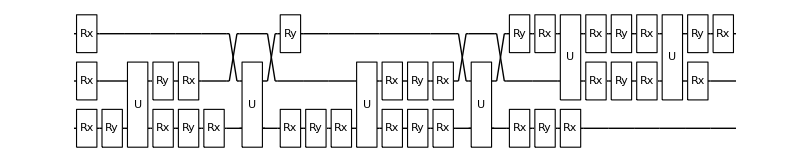

{Rx_1[-1.981],Rx_2[-2.6423],Ry_1[π/2],Ry_2[π/2],CZG_(0,1),Rx_0[π/2],Ry_0[π/4],Rx_0[-π/2],Rx_1[π/2],Ry_1[3.0061],Rx_1[π/2],CZG_(0,2),Rx_0[-π/2],Ry_0[π/4],Rx_0[-π/2],Rx_2[-π/2],Rx_2[2.702],Rx_2[π/2],CZG_(0,1),Rx_0[π/2],Ry_0[(3 π)/4],Rx_1[-2.7048],Ry_1[0.89527],Rx_0[π/2],Rx_1[0.92944],CZG_(0,2),Rx_0[-π/2],Ry_0[π/4],Rx_0[π/2],Rx_2[-π/2],Ry_2[0.93891],CZG_(1,2),Rx_1[π/2],Ry_1[π/2],Rx_1[π/2],Rx_2[π/4],Ry_2[π/2],Rx_2[-π/2],CZG_(1,2),Rx_1[-π/2],Ry_1[π/4],Rx_1[-π/2],Rx_2[π/2]}

{Rx_1[-1.981],Rx_2[-2.6423],Ry_1[π/2],Ry_2[π/2],CZG_(0,1),Rx_0[π/2],Ry_0[π/4],Rx_0[-π/2],Rx_1[π/2],Ry_1[3.0061],Rx_1[π/2],CZG_(0,2),Rx_0[-π/2],Ry_0[π/4],Rx_0[-π/2],Rx_2[-π/2],Ry_2[2.702],Rx_2[π/2],CZG_(0,1),Rx_0[π/2],Ry_0[(3 π)/4],Rx_1[-2.7048],Ry_1[0.89527],Rx_0[π/2],Rx_1[0.92944],CZG_(0,2),Rx_0[-π/2],Ry_0[π/4],Rx_0[π/2],Rx_2[-π/2],Ry_2[0.93891],CZG_(1,2),Rx_1[π/2],Ry_1[π/2],Rx_1[π/2],Rx_2[π/4],Ry_2[π/2],Rx_2[-π/2],CZG_(1,2),Rx_1[-π/2],Ry_1[π/4],Rx_1[-π/2],Rx_2[π/2]}

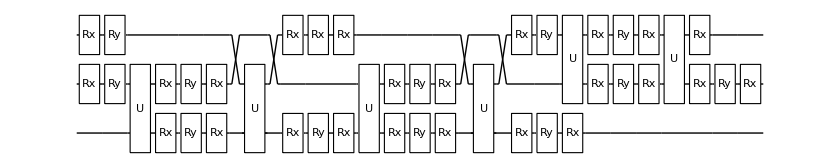

InsertCircuitNoise::error: Encountered gate CZ_(0,1) which is not supported by the given device specification. Note this may be due to preceding gates, if the spec contains constraints which depend on dynamic variables. See ?GetUnsupportedGates.

ExtractCircuit::error: Invalid arguments. See ?ExtractCircuit

CalcCircuitMatrix::error: Invalid arguments. See ?CalcCircuitMatrix

```mathematica
TGate[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][-Pi/4],Subscript[Rx, t][-Pi/2]}
Tdg[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][Pi/4],Subscript[Rx, t][-Pi/2]}

CCZDecomp[t_,c1_,c2_]:={Subscript[Rx, t][-0.09065988720074536],Subscript[Ry, t][-Pi/2],Subscript[Rx, c1][-Pi],Subscript[Rx, c2][-Pi],Subscript[CZG, t,c1],Subscript[Rx, t][-0.800360109933159],Subscript[Ry, t][1.372292382481866],Subscript[Rx, t][1.63614359593572],Subscript[Ry, c1][-Pi],Subscript[Rx, c1][-Pi],Subscript[CZG, t,c2],Subscript[Rx, t][2.3583],Subscript[Ry, t][0.82493],Subscript[Rx, t][-2.7641],Subscript[Ry, c2][Pi],Subscript[CZG, t,c1],Subscript[Rx, t][-0.12796],Subscript[Ry, t][0.68257],Subscript[Rx, t][-2.5412],Subscript[Rx, c1][-π/2],Subscript[Ry, c1][Pi/4],Subscript[Rx, c1][-π/2],Subscript[CZG, t,c2],Subscript[Rx, t][-2.7055],Subscript[Ry, t][2.2467],Subscript[Rx, t][2.211],Subscript[Ry, c2][-π/2],Subscript[Rx, c2][Pi/2],Subscript[CZG, c1,c2],Subscript[Rx, c1][π/2],Subscript[Ry, c1][Pi/2],Subscript[Rx, c1][Pi/2],Subscript[Rx, c2][Pi/4],Subscript[Ry, c2][Pi/2],Subscript[Rx, c2][-Pi/2],Subscript[CZG, c1,c2],Subscript[Rx, c1][-Pi],Subscript[Ry, c2][-Pi/4],Subscript[Rx, c2][-Pi/2]};

DrawCircuit[ExtractCircuit[GetCircuitSchedule[CCZDecomp[0,1,2],RydDev,ReplaceAliases->True]]]//MatrixForm
```

```mathematica
?QuEST`*
```